## Project

## Segmentation

### Image

### Importing the video to variable video

```mathematica
video = Import["/Users/aryandawer7/Desktop/Wolfram/Main/First Date – Hyundai Super Bowl Commercial _ The Hyundai Genesis--R_483zeVF8.mp4"];
```

### Extracting all the frames in the video

```mathematica
frameList = AssociationThread[Range[Length[VideoFrameList[video, All]]]->VideoFrameList[video, All]];
```

```mathematica
(*frameListShort = First/@Split[Values[frameList],ImageDistance[#1,#2]<=300&]*)
```

### Finding Faces within the extracted frames

```mathematica
faceList = DeleteCases[FindFaces[#, "Image"]&/@frameList,{}]
```

### Classifier function to segment frames based on faces

```mathematica
chars = {-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
fr = FaceRecognize[{-Graphics-->"char1",-Graphics--> "char2",-Graphics-->"char3"}]
```

### Converting into a rule that where every face box is attached to its frame

```mathematica
splitValues[key_,values_]:=key->#&/@values
faceList = Flatten[KeyValueMap[splitValues,faceList]]
```

### Grouping all the frames in order according to face

```mathematica
seperateFaceList = GroupBy[faceList,fr[Last[#]]&]
```

### Dropping the face frames that couldn’t be classified

```mathematica
seperateFaceList = KeyDrop[seperateFaceList,Missing["Anomalous"]]
```

```mathematica
order = Last/@Characters/@Keys[seperateFaceList]
```

### Getting segmented lists without frame numbers

```mathematica
expressionsKeys = ToExpression["char"<>ToString[#]<>"Faces"]&/@order
```

```mathematica
expressionsVals = Table[Table[seperateFaceList[[n]][[x]][[2]],{x,1,Length[seperateFaceList[[n]]]}],{n,1,3}]
```

```mathematica
expressions = AssociationThread[expressionsKeys->expressionsVals]
```

### Audio/Text

### Storing audio of the commercial as text

```mathematica
textInVideo = Import["/Users/aryandawer7/Desktop/Wolfram/Main/First Date – Hyundai Super Bowl Commercial _ The Hyundai Genesis--R_483zeVF8.en.vtt"];
```

### Preprocessing functions to handle imported audio

```mathematica
stringToTimeObjs[inpStr_String] := Last[ToExpression/@StringSplit[inpStr,":"]]
```

```mathematica
preProcessText[allText_] := Replace[#,{a_,b__}:>{stringToTimeObjs[First[StringSplit[a]]],stringToTimeObjs[StringSplit[a][[3]]],StringReplace[StringRiffle@{b},Shortest["<"~~___~~">"]->""]}]&/@StringSplit[Select[Select[StringTrim[StringSplit[StringSplit[allText,StartOfLine~~EndOfLine] ,StartOfLine~~Whitespace~~EndOfLine]//Flatten], StringContainsQ[#,StartOfString~~DigitCharacter~~DigitCharacter~~":"~~DigitCharacter~~DigitCharacter~~":"~~DigitCharacter~~DigitCharacter~~"."~~DigitCharacter~~DigitCharacter~~DigitCharacter]&],StringContainsQ[#,"\n"]&],"\n"]
```

### Storing preprocessing output

```mathematica
processedText = preProcessText[textInVideo]
```

```mathematica
timeAndTextAssoc = AssociationThread[Table[Interval@{processedText[[x,1]],processedText[[x,2]]},{x,1,Length[processedText]}]->Table[{processedText[[x,3]],First[Classify["Sentiment"][processedText[[x,3]],"TopProbabilities"]]},{x,1.Length[processedText]}]]
```

## Analysis

### Getting a given number of images for analysis from each character’s dataset

```mathematica
lisOfFrames[characterFaceList_] := Table[characterFaceList[[x]],{x,1,Length[characterFaceList],Round[Length[characterFaceList]/10]}]
```

```mathematica
(*getLabels[frames_,character_] := AssociationMap[Reverse,frames]/@seperateFaceList[character]*)
```

```mathematica
(*Alternative----kidFaceFrameList = First/@Split[kidFaces,ImageDistance[#1,#2]<=60&];*)
```

### WordCloud Implementation

#### Finding scene changes in the commercial

```mathematica
char1List = lisOfFrames[expressions[char1Faces]]
```

```mathematica
char2List = lisOfFrames[expressions[char2Faces]]
```

```mathematica
char3List = lisOfFrames[expressions[char3Faces]]
```

#### Using functions above for data preprocessing

Character1

```mathematica
initial1 =(Classify["FacialExpression"][char1List,"TopProbabilities"->All])
```

```mathematica
ppl1 = GroupBy[initial1//Flatten,First[#]&]
```

```mathematica
eppl1 = Total[Last/@#]&/@ppl1
```

```mathematica
final1 = KeyDrop[eppl1,Entity["Emotion","Neutral::7468h"]]
```

Character2

```mathematica
initial2 =(Classify["FacialExpression"][char2List,"TopProbabilities"->All])
```

```mathematica
ppl2 = GroupBy[initial2//Flatten,First[#]&]
```

```mathematica
eppl2 = Total[Last/@#]&/@ppl2
```

```mathematica
final2 = KeyDrop[eppl2,Entity["Emotion","Neutral::7468h"]]
```

Character3

```mathematica
initial3 = (Classify["FacialExpression"][char3List,"TopProbabilities"->All])
```

```mathematica
ppl3 = GroupBy[initial3//Flatten,First[#]&]
```

```mathematica
eppl3 = Total[Last/@#]&/@ppl3
```

```mathematica
final3 = KeyDrop[eppl3,Entity["Emotion","Neutral::7468h"]]
```

```mathematica
emoClouds = WordCloud/@{final1,final2,final3}
```

### TimeLine Implementation

#### Associating face image with emotion identified

```mathematica
FaceEmotionConnect = AssociationThread[({char1List,char2List,char3List}//Flatten)->Keys[First/@Normal[KeyDrop[Join[initial1,initial2,initial3],Entity["Emotion","Neutral::7468h"]]]]]
```

```mathematica
lisFaceEmotionConnect = Normal[FaceEmotionConnect];
```

#### Associating previous list with character labels

```mathematica
labelAppen [a_->b_]:= (x = fr[a];{x,a->b});
```

```mathematica
valueListForTime = labelAppen/@lisFaceEmotionConnect
```

#### Getting frame numbers and converting them to timestamps

```mathematica
frameRate = Length[frameList]/Duration[video]
```

```mathematica
framesBlaBla =Association[Reverse/@faceList]/@ Keys[FaceEmotionConnect]/frameRate
```

#### Associating the FacialEmotionConnect with the timestamp of expression’s occurrence

```mathematica
lisWithTime = AssociationThread[framesBlaBla->valueListForTime]
```

#### Using functions above for data preprocessing

```mathematica
charSplitTimeData =GatherBy[Normal[lisWithTime],Values[#][[1]]&]
```

Character1

```mathematica
emoGrouped1 =Association/@Reverse/@GatherBy[charSplitTimeData[[1]],Values[#][[2,2]]&]
```

```mathematica
pictures1 = (Cases[#,r_Rule:>Thumbnail@First@r,Infinity]&/@ Values[emoGrouped1]);
```

```mathematica
emotions1 = Keys[emoGrouped1];
```

```mathematica
plot1 = TimelinePlot[Tooltip@@@ReplaceAll[#,q_Quantity:>QuantityMagnitude@q]&/@(Transpose/@Partition[Riffle[emotions1,pictures1],2]),PlotLegends->Last@*Last/@Last/@Values[emoGrouped1],Spacings->None]
```

Character2

```mathematica
emoGrouped2 = Association/@Reverse/@GatherBy[charSplitTimeData[[2]],Values[#][[2,2]]&]
```

```mathematica
pictures2 = (Cases[#,r_Rule:>Thumbnail@First@r,Infinity]&/@ Values[emoGrouped2]);
```

```mathematica
emotions2 = Keys[emoGrouped2];
```

```mathematica
plot2 = TimelinePlot[Tooltip@@@ReplaceAll[#,q_Quantity:>QuantityMagnitude@q]&/@(Transpose/@Partition[Riffle[emotions2,pictures2],2]),PlotLegends->Last@*Last/@Last/@Values[emoGrouped2],Spacings->None]
```

Character3

```mathematica
emoGrouped3 = Association/@Reverse/@GatherBy[charSplitTimeData[[3]],Values[#][[2,2]]&]
```

```mathematica
pictures3 = (Cases[#,r_Rule:>Thumbnail@First@r,Infinity]&/@ Values[emoGrouped3]);
```

```mathematica
emotions3 = Keys[emoGrouped3];
```

```mathematica
plot3 = TimelinePlot[Tooltip@@@ReplaceAll[#,q_Quantity:>QuantityMagnitude@q]&/@(Transpose/@Partition[Riffle[emotions3,pictures3],2]),PlotLegends->Last@*Last/@Last/@Values[emoGrouped3],Spacings->None]
```

```mathematica
plots = {plot1,plot2,plot3}
```

AllCharacters

```mathematica
allCharactersMessy = Join[emoGrouped1,emoGrouped2,emoGrouped3]
```

```mathematica
allCharsInAssoc = Association/@GatherBy[Normal[Association[allCharactersMessy]],Values[#][[2,2]]&]
```

```mathematica
allPictures = (Cases[#,r_Rule:>Thumbnail@First@r,Infinity]&/@ Values[allCharsInAssoc]);
```

```mathematica
allEmotions = Keys[allCharsInAssoc];
```

```mathematica
plotAll = TimelinePlot[Tooltip@@@ReplaceAll[#,q_Quantity:>QuantityMagnitude@q]&/@(Transpose/@Partition[Riffle[allEmotions,allPictures],2]),PlotLegends->Last@*Last/@Last/@Values[allCharsInAssoc],Spacings->None]
```

### Text TimeLine Implementation

#### Gathering all intervals based on emotion represented and finding legend list

```mathematica
gatheredText =Association/@GatherBy[Normal[timeAndTextAssoc],Values[#][[2,1]]&]
```

```mathematica
legend = First/@Last/@Last/@Values[gatheredText]
```

#### Using processed data to plot

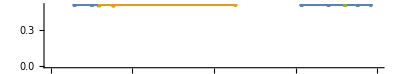

```mathematica
nmlplt = NumberLinePlot[ Keys/@gatheredText,{x,0,60},Spacings->{0.5,0,0},PlotLegends->legend]
```

## Results

### Presenting the processed information in the form of WordClouds or EmotionClouds (if I may)

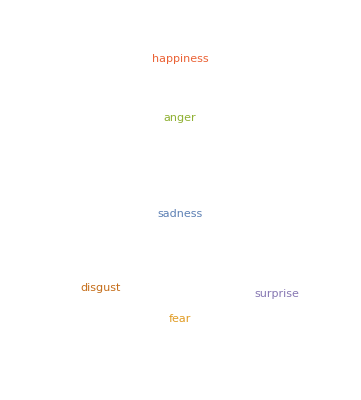
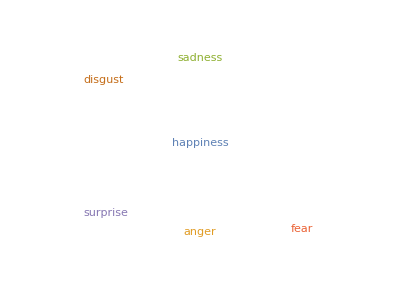
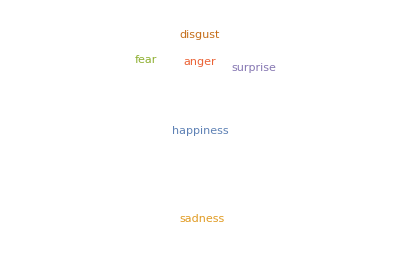
<|-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-|>

```mathematica
AssociationThread[chars->emoClouds]
```

### Presenting the processed information in the form of a timeline of the commercial

#### Plotting individual timelines for characters

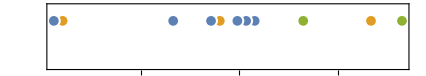
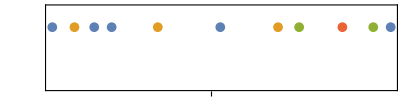
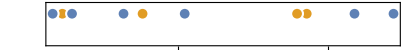
<|-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-|>

```mathematica
AssociationThread[chars->plots]
```

#### Plotting a single timeline for the whole advertisement

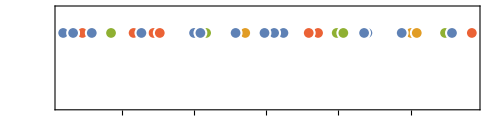

```mathematica
plotAll
```

### Presenting the results of audio/text analysis on a timeline

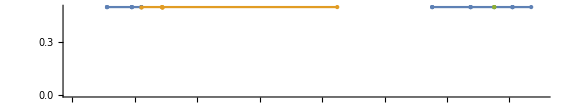

```mathematica
nmlplt
```